```mathematica
SetDirectory["/home/dschiebe/Documents/lanayru/PhD_Files/HexaBox_102PureIntsDone"];
PureIntegralsOld=ReadList[FileNameJoin[{Directory[],"files/LinearBasis-169.txt"}]];
PureIntegralsNew=PureIntegralsOld;
Get[FileNameJoin[{Directory[],"HexaBoxModules.m"}]];
$P=2^31-1;
$P=2^31-1;
CayleyEntry[i_,j_]:=Module[{mat},
If[i==0 && j==0 ,
Return[0];
];
If[i==0 || j==0 ,
Return[1];
];

If[i==j,
mat=2msq[i]/.intMasses;
Return[mat];
];
If[i<j,
mat=((msq[i]/.intMasses)+(msq[j]/.intMasses)-Expand[(Sum[q[n],{n,i,j-1}])^2])/.mandelstamScalarProducts/.kinematics;
Return[mat];
];
If[i>j,
mat=CayleyEntry[j,i];
Return[mat];
];
]
cutCayley[mat_,l_]:=Module[{res},
res=mat;
res=Delete[res,l];
res=Transpose[Delete[Transpose[res],l]];
res
]
```

# Gram Change

```mathematica
CanonicalGramVec={p[1],p[2],p[3],p[4]};
Ganonical5ptGram=16Det[Expand[Table[CanonicalGramVec[[i]]CanonicalGramVec[[j]],{i,1,4},{j,1,4}]]/.kinematics/.mandelstamScalarProducts]//Factor
vectors={p[3],p[4],p[5],p[6]};
Gram1=16Det[Expand[Table[vectors[[i]]vectors[[j]],{i,1,4},{j,1,4}]/.p4cons]/.kinematics/.mandelstamScalarProducts]//Factor;
GramChange1=16Det[Expand[Table[vectors[[i]]CanonicalGramVec[[j]],{i,1,4},{j,1,4}]/.p4cons]/.kinematics/.mandelstamScalarProducts]//Factor;

vectors={p[4],p[5],p[6],p[1]};
Gram2=16Det[Expand[Table[vectors[[i]]vectors[[j]],{i,1,4},{j,1,4}]/.p4cons]/.kinematics/.mandelstamScalarProducts]//Factor;
GramChange2=16Det[Expand[Table[vectors[[i]]CanonicalGramVec[[j]],{i,1,4},{j,1,4}]/.p4cons]/.kinematics/.mandelstamScalarProducts]//Factor;

vectors={p[5],p[6],p[1],p[2]};
Gram3=16Det[Expand[Table[vectors[[i]]vectors[[j]],{i,1,4},{j,1,4}]/.p4cons]/.kinematics/.mandelstamScalarProducts]//Factor;
GramChange3=16Det[Expand[Table[vectors[[i]]CanonicalGramVec[[j]],{i,1,4},{j,1,4}]/.p4cons]/.kinematics/.mandelstamScalarProducts]//Factor;

vectors={p[3],p[2],p[1],p[6]};
Gram4=16Det[Expand[Table[vectors[[i]]vectors[[j]],{i,1,4},{j,1,4}]/.p4cons]/.kinematics/.mandelstamScalarProducts]//Factor;
GramChange4=16Det[Expand[Table[vectors[[i]]CanonicalGramVec[[j]],{i,1,4},{j,1,4}]/.p4cons]/.kinematics/.mandelstamScalarProducts]//Factor;

vectors={p[2],p[3],p[4],p[5]};
Gram5=16Det[Expand[Table[vectors[[i]]vectors[[j]],{i,1,4},{j,1,4}]/.p4cons]/.kinematics/.mandelstamScalarProducts]//Factor;
GramChange5=16Det[Expand[Table[vectors[[i]]CanonicalGramVec[[j]],{i,1,4},{j,1,4}]/.p4cons]/.kinematics/.mandelstamScalarProducts]//Factor;

vectors={p[3],p[4],p[5],p[6]};
Gram6=16Det[Expand[Table[vectors[[i]]vectors[[j]],{i,1,4},{j,1,4}]/.p4cons]/.kinematics/.mandelstamScalarProducts]//Factor;
GramChange6=16Det[Expand[Table[vectors[[i]]CanonicalGramVec[[j]],{i,1,4},{j,1,4}]/.p4cons]/.kinematics/.mandelstamScalarProducts]//Factor;


Gram5Repl={root[Gram1]->GramChange1/root[Ganonical5ptGram],root[Gram2]->GramChange2/root[Ganonical5ptGram],root[Gram3]->GramChange3/root[Ganonical5ptGram],root[Gram4]->GramChange4/root[Ganonical5ptGram],root[Gram5]->GramChange5/root[Ganonical5ptGram],root[Gram6]->GramChange6/root[Ganonical5ptGram]};
```

s12^2 s23^2-2 s12^2 s23 s234+2 s12 s123 s23 s234+s12^2 s234^2-2 s12 s123 s234^2+s123^2 s234^2+2 s12 s123 s23 s34-2 s12 s23^2 s34+2 s12 s123 s234 s34-2 s123^2 s234 s34+2 s12 s23 s234 s34+2 s123 s23 s234 s34+s123^2 s34^2-2 s123 s23 s34^2+s23^2 s34^2-2 s12 s23^2 s56+2 s12 s23 s234 s56-2 s123 s23 s234 s56-4 s12 s23 s34 s56+2 s123 s23 s34 s56-2 s23^2 s34 s56+s23^2 s56^2

# Diagram 179 (BasisL -169 )

hxb[1,0,1,1,0,0,1,1,1,0,0,0,0]

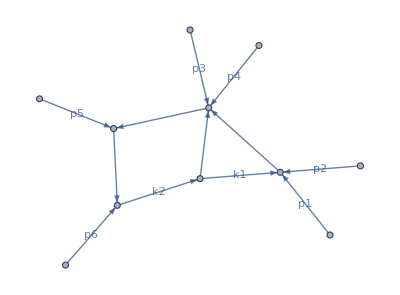

```mathematica
PureIntegralsOld[[179]]
plotDiagram[PureIntegralsOld[[179]]]
```

```mathematica
(*v12=Expand[Expand[2(p[5]*p[6])/.p4cons]/.kinematics/.mandelstamScalarProducts]
vectors={p[1]+p[2],p[5]+p[3]+p[4]};
DetGram=Expand[-4Det[Table[Expand[vectors[[i]]vectors[[j]]/.p4cons]/.kinematics/.mandelstamScalarProducts,{i,1,2},{j,1,2}]]]*)
BasisChange[1]=ep^4
```

ep^4

# Diagram 180 (BasisL -169 )

hxb[1,0,1,1,0,1,0,1,1,0,0,0,0]

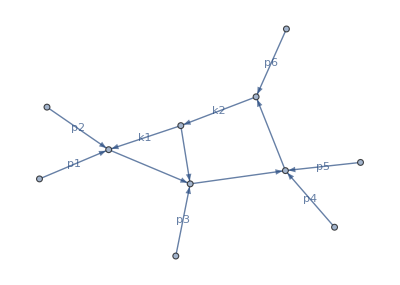

```mathematica
PureIntegralsOld[[180]]
plotDiagram[PureIntegralsOld[[180]]]
```

```mathematica
v12=Expand[Expand[2(p[6]*(p[5]+p[4]))/.p4cons]/.kinematics/.mandelstamScalarProducts]
vectors={p[1]+p[2],p[5]+p[3]+p[4]};
DetGram=Expand[-4Det[Table[Expand[vectors[[i]]vectors[[j]]/.p4cons]/.kinematics/.mandelstamScalarProducts,{i,1,2},{j,1,2}]]]
BasisChange[2]=ep^4(*(v12)root[DetGram]*)
```

-mt2+s123-s45

mt2^2-2 mt2 s12+s12^2-2 mt2 s345-2 s12 s345+s345^2

ep^4

# Diagram 186 (BasisL -169 )

hxb[1,0,1,1,1,0,1,1,0,0,0,0,0]

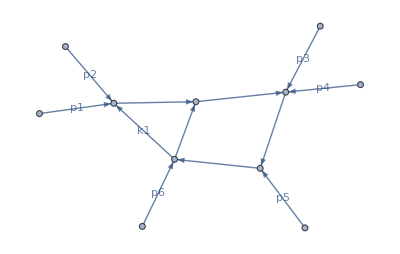

```mathematica
PureIntegralsOld[[186]]
plotDiagram[PureIntegralsOld[[186]]]
```

```mathematica
BasisChange[3]=ep^4
```

# Diagram 187 (BasisL -169 )

hxb[1,0,1,1,1,1,0,1,0,0,0,0,0]

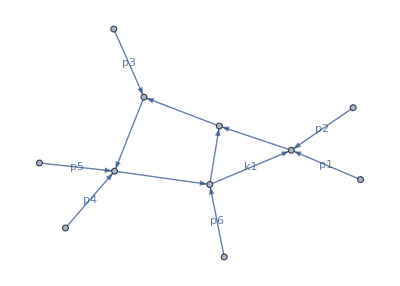

```mathematica
PureIntegralsOld[[187]]
plotDiagram[PureIntegralsOld[[187]]]
```

```mathematica
BasisChange[4]=ep^4
```

ep^4

# Diagram 187 (BasisL -169 )

hxb[-1,1,1,1,0,0,1,1,1,0,0,0,0]

hxb[0,1,1,1,0,0,1,1,1,0,0,0,0]

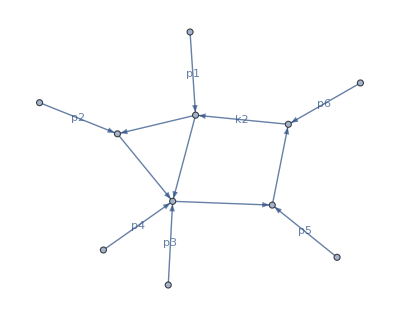

```mathematica
PureIntegralsOld[[170]]
PureIntegralsOld[[174]]
plotDiagram[PureIntegralsOld[[174]]]
```

```mathematica
BasisChange[5,1]=ep^4
BasisChange[5,2]=ep^3/PR[4]
```

ep^4

ep^3/PR[4]

# Diagram 196, 203, 205, 206, 207 (BasisL -169 )

```mathematica
PureIntegralsOld[[196]]
PureIntegralsOld[[203]]
PureIntegralsOld[[205]]
PureIntegralsOld[[206]]
PureIntegralsOld[[207]]
plotDiagram[PureIntegralsOld[[174]]]
```

hxb[1,1,1,1,-1,0,1,1,0,0,0,0,0]

hxb[1,1,1,1,0,-1,1,1,0,0,0,0,0]

hxb[1,1,1,1,0,0,1,1,-1,0,0,0,0]

hxb[1,1,1,1,0,0,1,1,0,-1,0,0,0]

hxb[1,1,1,1,0,0,1,1,0,0,0,0,0]

-Graphics-

```mathematica
BasisChange[11,1]=ep^4
BasisChange[11,2]=ep^3*(3-d)
BasisChange[11,3]=ep^3/PR[4]
```

ep^4

(3-d) ep^3

ep^3/PR[4]

# Assemble basis

```mathematica
SelectInts={2,3,4,7,8,9,10,11,12,14,15,16,17,18,19,20,21,22,23,24,28,32,34,35,36,37,38,39,40,41,42,43,44,45,46,47,75,76,77,78,79,80,81,82,83,84,85,86,87,88,91,92,94,95,96,97,98,103,104,105,107,112,113,114,115,116,117,118,119,120,121,122,123,124,125,126,127,128,129,130,131,132,133,134,135,136,137,138,152,153,154,155,156,157,158,159,160,161,162,163,164,165,166,167,168,169,179,180,186,187,170,174,171,175,172,176,189,190,191,192,193,194,196,203,205,206,207,177,178,181,182,183,184,198,210,212,213,214,215}

SelectIntsNotPure=Pick[SelectInts,Thread[SelectInts>169]]
SelectIntsPure=Pick[SelectInts,Thread[SelectInts<=169]];
PureIntegralsNew=PureIntegralsOld;


PureIntegralsNew[[179]]=Collect[PureIntegralsOld[[179]]*BasisChange[1]//Expand,{_hxb,root[___]},Together];
PureIntegralsNew[[180]]=Collect[PureIntegralsOld[[180]]*BasisChange[2]//Expand,{_hxb,root[___]},Together];
PureIntegralsNew[[186]]=Collect[PureIntegralsOld[[186]]*BasisChange[3]//Expand,{_hxb,root[___]},Together];
PureIntegralsNew[[187]]=Collect[PureIntegralsOld[[187]]*BasisChange[4]//Expand,{_hxb,root[___]},Together];

PureIntegralsNew[[170]]=Collect[PureIntegralsOld[[174]]*BasisChange[5,1]//Expand,{_hxb,root[___]},Together];
PureIntegralsNew[[174]]=Collect[PureIntegralsOld[[174]]*BasisChange[5,2]//Expand,{_hxb,root[___]},Together];
PureIntegralsNew[[171]]=Collect[PureIntegralsOld[[175]]*BasisChange[5,1]//Expand,{_hxb,root[___]},Together];
PureIntegralsNew[[175]]=Collect[PureIntegralsOld[[175]]*BasisChange[5,2]//Expand,{_hxb,root[___]},Together];
PureIntegralsNew[[172]]=Collect[PureIntegralsOld[[176]]*BasisChange[5,1]//Expand,{_hxb,root[___]},Together];
PureIntegralsNew[[176]]=Collect[PureIntegralsOld[[176]]*BasisChange[5,2]//Expand,{_hxb,root[___]},Together];
PureIntegralsNew[[189]]=Collect[PureIntegralsOld[[190]]*BasisChange[5,1]//Expand,{_hxb,root[___]},Together];
PureIntegralsNew[[190]]=Collect[PureIntegralsOld[[190]]*BasisChange[5,2]//Expand,{_hxb,root[___]},Together];
PureIntegralsNew[[191]]=Collect[PureIntegralsOld[[192]]*BasisChange[5,1]//Expand,{_hxb,root[___]},Together];
PureIntegralsNew[[192]]=Collect[PureIntegralsOld[[192]]*BasisChange[5,2]//Expand,{_hxb,root[___]},Together];
PureIntegralsNew[[193]]=Collect[PureIntegralsOld[[194]]*BasisChange[5,1]//Expand,{_hxb,root[___]},Together];
PureIntegralsNew[[194]]=Collect[PureIntegralsOld[[194]]*BasisChange[5,2]//Expand,{_hxb,root[___]},Together];

(*PureIntegralsNew[[196]]=Collect[PureIntegralsOld[[207]]*BasisChange[11,1]//Expand,{_hxb,root[___]},Together];
PureIntegralsNew[[203]]=Collect[PureIntegralsOld[[207]]*BasisChange[11,2]//Expand,{_hxb,root[___]},Together];
PureIntegralsNew[[205]]=Collect[PureIntegralsOld[[207]]*BasisChange[11,3]//Expand,{_hxb,root[___]},Together];
PureIntegralsNew[[206]]=Collect[PureIntegralsOld[[207]]*BasisChange[11,4]//Expand,{_hxb,root[___]},Together];
PureIntegralsNew[[207]]=Collect[PureIntegralsOld[[207]]*BasisChange[11,1]//Expand,{_hxb,root[___]},Together];
*)
PureIntegralsNew[[207]]=Collect[PureIntegralsOld[[207]]*BasisChange[11,1]//Expand,{_hxb,root[___]},Together];
PureIntegralsNew[[206]]=Collect[PureIntegralsOld[[206]]*BasisChange[11,1]//Expand,{_hxb,root[___]},Together];
PureIntegralsNew[[205]]=Collect[PureIntegralsOld[[205]]*BasisChange[11,2]//Expand,{_hxb,root[___]},Together];
PureIntegralsNew[[203]]=Collect[PureIntegralsOld[[203]]*BasisChange[11,2]//Expand,{_hxb,root[___]},Together];
PureIntegralsNew[[196]]=Collect[PureIntegralsOld[[196]]*BasisChange[11,2]//Expand,{_hxb,root[___]},Together];

PureIntegralsNew[[177]]=Collect[PureIntegralsOld[[177]]*BasisChange[11,2]//Expand,{_hxb,root[___]},Together];
PureIntegralsNew[[178]]=Collect[PureIntegralsOld[[178]]*BasisChange[11,1]//Expand,{_hxb,root[___]},Together];
PureIntegralsNew[[181]]=Collect[PureIntegralsOld[[181]]*BasisChange[11,1]//Expand,{_hxb,root[___]},Together];
PureIntegralsNew[[182]]=Collect[PureIntegralsOld[[182]]*BasisChange[11,2]//Expand,{_hxb,root[___]},Together];
PureIntegralsNew[[183]]=Collect[PureIntegralsOld[[183]]*BasisChange[11,2]//Expand,{_hxb,root[___]},Together];
PureIntegralsNew[[184]]=Collect[PureIntegralsOld[[184]]*BasisChange[11,1]//Expand,{_hxb,root[___]},Together];

PureIntegralsNew[[198]]=Collect[PureIntegralsOld[[198]]*BasisChange[11,2]//Expand,{_hxb,root[___]},Together];
PureIntegralsNew[[210]]=Collect[PureIntegralsOld[[210]]*BasisChange[11,2]//Expand,{_hxb,root[___]},Together];
PureIntegralsNew[[212]]=Collect[PureIntegralsOld[[212]]*BasisChange[11,2]//Expand,{_hxb,root[___]},Together];
PureIntegralsNew[[213]]=Collect[PureIntegralsOld[[213]]*BasisChange[11,1]//Expand,{_hxb,root[___]},Together];
PureIntegralsNew[[214]]=Collect[PureIntegralsOld[[214]]*BasisChange[11,1]//Expand,{_hxb,root[___]},Together];
PureIntegralsNew[[215]]=Collect[PureIntegralsOld[[215]]*BasisChange[11,1]//Expand,{_hxb,root[___]},Together];

SubPureInts=PureIntegralsNew[[SelectInts]](*/.Gram5Repl*);
Newsqrts=(Cases[SubPureInts,root[___],Infinity]//DeleteDuplicates)/.root[x_]:>x
Oldsqrts=(Cases[PureIntegralsOld(*/.Gram5Repl*),root[___],Infinity]//DeleteDuplicates)/.root[x_]:>x
sqrtSetNew=Join[Oldsqrts,Newsqrts]//DeleteDuplicates;
Export[FileNameJoin[{Directory[],"files/Roots.txt"}],sqrtSetNew];
Export[FileNameJoin[{NotebookDirectory[],"TrianglePureInts.txt"}],SubPureInts];
```

{2,3,4,7,8,9,10,11,12,14,15,16,17,18,19,20,21,22,23,24,28,32,34,35,36,37,38,39,40,41,42,43,44,45,46,47,75,76,77,78,79,80,81,82,83,84,85,86,87,88,91,92,94,95,96,97,98,103,104,105,107,112,113,114,115,116,117,118,119,120,121,122,123,124,125,126,127,128,129,130,131,132,133,134,135,136,137,138,152,153,154,155,156,157,158,159,160,161,162,163,164,165,166,167,168,169,179,180,186,187,170,174,171,175,172,176,189,190,191,192,193,194,196,203,205,206,207,177,178,181,182,183,184,198,210,212,213,214,215}

{179,180,186,187,170,174,171,175,172,176,189,190,191,192,193,194,196,203,205,206,207,177,178,181,182,183,184,198,210,212,213,214,215}

{(-s12+s34)^2-2 (s12+s34) s56+s56^2,-4 mt2 s12+(-mt2-s12+s345)^2,-4 mt2 s56+s56^2,mt2^2-2 mt2 s123+s123^2-2 mt2 s45-2 s123 s45+s45^2,mt2^2-2 mt2 s34+s34^2-2 mt2 s345-2 s34 s345+s345^2,s345^2-2 s345 s45+s45^2,mt2^2-2 mt2 s16+s16^2-2 mt2 s234-2 s16 s234+s234^2,s16^2-2 s16 s23+s23^2-2 s16 s45-2 s23 s45+s45^2,s56 (-4 mt2 s12 s34+(mt2-s345)^2 s56),s56 (-4 mt2 s12 s34+mt2^2 s56-2 mt2 s345 s56+s345^2 s56)}

{(-s12+s34)^2-2 (s12+s34) s56+s56^2,-4 s12 s23 s34 (-s123+s23-s234+s56)+(-s12 s23+s12 s234-s123 s234+s123 s34-s23 s34+s23 s56)^2,-4 mt2 s12+(-mt2-s12+s345)^2,-4 mt2 s56+s56^2,mt2^2-2 mt2 s123+s123^2-2 mt2 s45-2 s123 s45+s45^2,mt2^2-2 mt2 s34+s34^2-2 mt2 s345-2 s34 s345+s345^2,-4 mt2 s12 s34 s56+mt2^2 s56^2-2 mt2 s345 s56^2+s345^2 s56^2,s12^2 s23^2-2 s12^2 s23 s234+2 s12 s123 s23 s234+s12^2 s234^2-2 s12 s123 s234^2+s123^2 s234^2+2 s12 s123 s23 s34-2 s12 s23^2 s34+2 s12 s123 s234 s34-2 s123^2 s234 s34+2 s12 s23 s234 s34+2 s123 s23 s234 s34+s123^2 s34^2-2 s123 s23 s34^2+s23^2 s34^2-2 s12 s23^2 s56+2 s12 s23 s234 s56-2 s123 s23 s234 s56-4 s12 s23 s34 s56+2 s123 s23 s34 s56-2 s23^2 s34 s56+s23^2 s56^2,s345^2-2 s345 s45+s45^2,mt2^2-2 mt2 s16+s16^2-2 mt2 s234-2 s16 s234+s234^2,s16^2-2 s16 s23+s23^2-2 s16 s45-2 s23 s45+s45^2,s56 (-4 mt2 s12 s34+(mt2-s345)^2 s56),s56 (-4 mt2 s12 s34+mt2^2 s56-2 mt2 s345 s56+s345^2 s56),(mt2 s12-mt2 s123+s123 s345-s12 s45)^2}

# Export New Basis

```mathematica
StillNonPureInts=DeleteElements[PureIntegralsOld[[170;;]],PureIntegralsOld[[SelectIntsNotPure]]];
NewPureInts=PureIntegralsNew[[SelectIntsNotPure]];
NewBasis=Join[PureIntegralsNew[[;;169]],NewPureInts,StillNonPureInts]//EchoFunction[Length];
NewBasis=NewBasis/.Gram5Repl;
Newsqrts=(Cases[NewBasis,root[___],Infinity]//DeleteDuplicates)/.root[x_]:>x
Export[FileNameJoin[{Directory[],"files/Roots.txt"}],Newsqrts];

Export[FileNameJoin[{Directory[],"files/LinearBasis-202.txt"}],NewBasis];
```

241

{(-s12+s34)^2-2 (s12+s34) s56+s56^2,-4 s12 s23 s34 (-s123+s23-s234+s56)+(-s12 s23+s12 s234-s123 s234+s123 s34-s23 s34+s23 s56)^2,-4 mt2 s12+(-mt2-s12+s345)^2,-4 mt2 s56+s56^2,mt2^2-2 mt2 s123+s123^2-2 mt2 s45-2 s123 s45+s45^2,mt2^2-2 mt2 s34+s34^2-2 mt2 s345-2 s34 s345+s345^2,-4 mt2 s12 s34 s56+mt2^2 s56^2-2 mt2 s345 s56^2+s345^2 s56^2,s12^2 s23^2-2 s12^2 s23 s234+2 s12 s123 s23 s234+s12^2 s234^2-2 s12 s123 s234^2+s123^2 s234^2+2 s12 s123 s23 s34-2 s12 s23^2 s34+2 s12 s123 s234 s34-2 s123^2 s234 s34+2 s12 s23 s234 s34+2 s123 s23 s234 s34+s123^2 s34^2-2 s123 s23 s34^2+s23^2 s34^2-2 s12 s23^2 s56+2 s12 s23 s234 s56-2 s123 s23 s234 s56-4 s12 s23 s34 s56+2 s123 s23 s34 s56-2 s23^2 s34 s56+s23^2 s56^2,s345^2-2 s345 s45+s45^2,mt2^2-2 mt2 s16+s16^2-2 mt2 s234-2 s16 s234+s234^2,s16^2-2 s16 s23+s23^2-2 s16 s45-2 s23 s45+s45^2,s56 (-4 mt2 s12 s34+(mt2-s345)^2 s56),s56 (-4 mt2 s12 s34+mt2^2 s56-2 mt2 s345 s56+s345^2 s56),(mt2 s12-mt2 s123+s123 s345-s12 s45)^2}

```mathematica
{152,153,154,155,156,157,158,159,160,161,162,163,164,165,166,167,168,169,170,172,174,176,177,178,179,180,181,182,183,184,186,187,189,190,191,192,193,194,196,198,203,205,206,207,210,212,213,214,215}//Length
```

49

```mathematica
SelectInts//Length
```

134

```mathematica
SymmetricDifference[SelectInts2,SelectInts]
```

{171,175}

```mathematica
{2,3,4,7,8,9,10,11,12,14,15,16,17,18,19,20,21,22,23,24,28,32,34,35,36,37,38,39,40,41,42,43,44,45,46,47,75,76,77,78,79,80,81,82,83,84,85,86,87,88,91,92,94,95,96,97,98,103,104,105,107,112,113,114,115,116,117,118,119,120,121,122,123,124,125,126,127,128,129,130,131,132,133,134,135,136,137,138,152,153,154,155,156,157,158,159,160,161,162,163,164,165,166,167,168,169,179,180,186,187,170,174,171,175,172,176,189,190,191,192,193,194,196,203,205,206,207,177,178,181,182,183,184,198,210,212,213,214,215}//Length
```

139

```mathematica
SelectIntsNotPure//Length
```

33

```mathematica
169+33
```

202